# Unitary visualisation

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## Visualising a unitary modules

### Trotterization-related modules

Reference:
https://aip.scitation.org/doi/10.1063/1.4768229

```mathematica
PauliCirc::usage="PauliCirc[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a term.";
PauliCirc[coef_,paulis_,nqubits_,factor_:1]:=Module[{circ,p,q,ngates},
If[Length@paulis>0,
circ=Table[
{p,q}=Level[c,-1];
Which[p===Z,{Subscript[C, q][Subscript[X, nqubits]]},p===X,{Subscript[Ry, q][π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Ry, q][-π/2]},p===Y,{Subscript[Rx, q][-π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Rx, q][π/2]}]
,{c,paulis}];
Join[circ,{{Subscript[Rz, nqubits][coef*factor]}},Reverse@circ]
,
circ={}
]
]


Propagator::usage="Propagator[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a propagator.";
Propagator[coef_,paulis_,factor_]:=Module[{lpaulis,p,q,ngates,ops,ids,rops,ropsd,rcnot,j,i,pauliops},
rops={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][-π/2], Subscript[Z, _]:>{}};
ropsd={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][π/2], Subscript[Z, _]:>{}};
rcnot={{i_Integer,j_Integer}:>Subscript[C, i][Subscript[X, j]] ,{{_Integer}}:>{} };
lpaulis=Table[{p,q}=Level[c,-1],{c,paulis}];
lpaulis=SortBy[lpaulis,#⟦2⟧&];
{ops,ids}={lpaulis⟦All,1⟧,Partition[lpaulis⟦All,2⟧,2,1]};
If[Length@ids<1, ids={lpaulis⟦All,2⟧}];
pauliops=Subscript[#⟦1⟧, #⟦2⟧]&/@lpaulis;
Flatten@{pauliops/.rops,ids/.rcnot,Subscript[Rz, Last@Last@ids][2*coef*factor],Reverse[ids/.rcnot],pauliops/.ropsd}
]


IsCommute::usage="IsCommute[List_paulis1, List_paulis2]. Return boolean indicates commutativity.";
IsCommute[P1_List,P2_List]:=Module[{m1,m2,nq,i},
nq=1+Max[Flatten@{P1,P2}/.Subscript[_, i_]->i];
m1=CalcCircuitMatrix[P1,nq];
m2=CalcCircuitMatrix[P2,nq];
If[Norm[m1.m2-m2.m1]≤10^-13,
True,
False]
]

PartitionPaulis::usage="ParititionPaulis[paulis], partition a list of pauli operators by commutation.";
PartitionPaulis[paulis_List]:=Module[{list1, list2},
list1={paulis⟦1⟧};list2={};
Table[
If[(AllTrue@@IsCommute[p⟦2;;⟧,#⟦2;;⟧]&/@list1)⟦1⟧,
AppendTo[list1,p],AppendTo[list2,p]]
,{p,paulis⟦2;;⟧}];
(*sanity checck*)
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list1,{2}]],
Print["ERR: there is a non-commuting operation in set A"]];
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list2,{2}]],
Print["ERR: there is a non-commuting operation in set B"]];
{list1,list2}
]

TrotterizeNaive::usage="TrotterizeNaive[hamiltonian_path, t, n]. Return the trotterization circuit, if full=False, it's not powered by n yet.";
TrotterizeNaive[hamfile_,t_,n_]:=Module[{ham,nqubits,nterms,r=N[t/n],estgates,esterr,circ},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,True];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
estgates=(2*Length@Flatten@ham-nterms)*n;
esterr=r^2//N;
circ=Flatten[Table[Propagator[paulis⟦1⟧,paulis⟦2;;⟧,r],{paulis,ham}],1];
Flatten@ConstantArray[circ,n]
]


Trotterize::usage="Trotterize[hamiltonian_path, t, n, order:1]. Return the trotterization circuit. Available up to the fourth order.
The paulis are partitioned into two sets A and B in which each element is commuting each other. 
Trotterization is available up to the 4th order
order 1: e^((A + B) t)=(e^(At/n)e^(Bt/n))^n+O(t Δt)
order 2: e^((A + B) t)=(e^(At/2  n)e^(Bt/n)e^(At/2  n))^n+O(t Δt^2)
order 2comp: is order 2 but compressed
order 2scb :(e^(At/2  n)e^(Bt/n)e^(At/2  n))(e^(Bt/2  n)e^(At/n)e^(Bt/2  n))(e^(At/2  n)e^(Bt/n)e^(At/2  n))
order 3: e^((A + B) t)=(e^(7/24)e^(2/3)e^(3/4)e^(-2/3)e^(-1/24)e^(Bt/n))^n+O(t Δt^3)
order 4: e^((A + B) t)=Π_(i = 1,  ... , 5)(e^p_ie^p_ie^p_i)^n+O(t Δt^4),where p1=p2=p4=p5=1/(4-4^(1/3)),p3=1-4p1
";
Trotterize[hamfile_,t_,n_,order_:1]:=Module[{ham,nterms,nqubits,list1,list2,Δt,f},
{ham,nterms,nqubits}=FormatHamiltonian[hamfile,True];
ham=DeleteCases[ham,{_}]; (*delete the global phase*)
{list1,list2}=PartitionPaulis[ham];
Which[
order===1,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===2,
f=N[0.5*t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
},{n}]
,
(*compressed2 -- check if it results in the circuit order 2
template: Flatten@{e^(A/2),e^B,Table[{e^A,e^B},{n-1}],e^(A/2)}
*)
order ==="2comp",
f=N[0.5*t/n];
Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[{Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}]},{n-1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
}
,
(*simon's version of order 2*)
order==="2scb",
f=N[0.5*t/n];
Flatten@Table[
If[OddQ@iter,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]}
,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]}]
,{iter,n}] 
,
order===3,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(7/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(2/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(3/4)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-2)/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-1)/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===4,
f=ConstantArray[N[1/(4-4^(1/3))],5];
f⟦3⟧=N[1-4f⟦1⟧];
f=(0.5*t/n)*f;
Flatten@Table[
Flatten[Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2#],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}]
}&/@f]
,{n}]
]
]
```

### Distance-related modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_,list_:False]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}:>{a Subscript[Id, 0]}};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
If[¬list,
{Total@Apply[Times,ham,1],nterms,nqubits}
,
{ham,nterms,nqubits}
]
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]

CountGates::usage="CountGates[circuit], return the count for {cnots, singles}";
CountGates[circuit_]:=Module[{cnotc},
cnotc=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{cnotc,Length@circuit-cnotc}
]

SetAttributes[MergeGates,HoldFirst]
MergeGates::usage="MergeGates[circuits], simplify circuits.";
MergeGates[circuits_]:=Module[{circc,circs,len,a,b,c,d,e,f,θ,j,i},
circs=Flatten@circuits;
While[True,
len=Length@circs;
circc=GetCircuitColumns[circuits];
circc=circc//.{
{a___,{b___,Subscript[H, j_],c___},{d___,Subscript[H, j_],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][-θ_],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][-θ_],c___},{d___,Subscript[Rx, j_][θ],e___},f___}:>{a,{b,c},{d,e},f},
{a___,{b___,Subscript[Rx, j_][θ_],c___},{d___,Subscript[Rx, j_][θ_],e___},f___}:>{a,{b,Subscript[Rx, j][2θ],c},{d,e},f},
{a___,{b___,Subscript[C, j_][Subscript[X, i_]],c___},{d___,Subscript[C, j_][Subscript[X, i_]],e___},f___}:>{a,{b,c},{d,e},f}
};
circs=Flatten@circc;
If[Length@circs===len,
Break[]]
];
circs
]

MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->2000,Method->"RandomSearch"];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]


distMatrices::usage="distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|> "
distMatrices[M1_,M2_,subspace_]:=Module[{globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];
{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
If[Length@subspace<Length@M1,
{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
,
{dfullsubopt,globalphase}={dfullopt,globalphase};
{dsubopt,globalphase}={dfullopt,globalphase}
];
<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]



GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace; 
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]
```

distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|>

## Data processing and module

### Load data

Recompilation: {cost, dist, ngates, minutes,ansatz, θvars, cycleres, [fev]}

```mathematica
ressubH2<<ressubH2.mx;
resfullH2<<resfullH2.mx;
```

Trotterization with distance in the subspace and full space: 
{{twos,singles},distance,entFid,<E(t)>err,Fiderr of psi(t)}

```mathematica
trotsumsub<<trotsumsub.mx;
trotsum<<trotsum.mx;
```

```mathematica
hampath="~/vqe/molecules/H2/H2.txt";
{hamiltonian,nterms,nqubits}=FormatHamiltonian[hampath]
```

{-0.0970663 Id_0-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3,15,4}

```mathematica
subspace={3,5,6,9,10,12}
fullspace=Range[2^nqubits]-1
times={0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}
```

{3,5,6,9,10,12}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

### The exact unitary visualisation

```mathematica
hammat=CalcPauliSumMatrix@hamiltonian;
```

```mathematica
matexact=<|Table[t->MatrixExp[-ⅈ hammat t],{t,times}]|>;
```

```mathematica
scheme=(Blend[{RGBColor[0.02,1,1],RGBColor[0,0.48,1],RGBColor[0,0,0.73],Black,RGBColor[0.6,0.22,0],RGBColor[1,0.55,0],White},Rescale[#1,{-1,1}]]&);
```

```mathematica
style[label_,epilog_]:={PlotTheme->"Detailed",PlotLabel->label,ImageSize->300,Epilog->Text[Style[epilog,20,White,Bold,FontFamily->"FreeSerif"],Scaled[{.5,.9}]],FrameStyle->Directive[Black,Medium],FrameTicks->All,ColorFunction->scheme,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{scheme[#]&,{-1,1}}],Bottom]}
```

### Visualise compilation cycles

Recompilation subspace : {cost, dist, ngates, minutes, ansatz, θvars, cycleres, [fev]}

```mathematica
times2={0.001,2,4};
```

```mathematica
matsubcomp=<|
Table[
dynmat=MatrixExp[-ⅈ hammat t];
Print["t=",t];
t->
Table[
Table[
circmat=If[Length@restrial[[7]]["ansatz"][[cycle]]>0,ConjugateTranspose@CalcCircuitMatrix[restrial[[7]]["ansatz"][[cycle]]/.restrial[[7]]["θvars"][[cycle]],nqubits],IdentityMatrix[2^nqubits]];
<|
"matrix"->circmat,
"ngates"->Length@restrial[[7]]["ansatz"][[cycle]]
,
"subdist"->MatrixDist[dynmat,circmat,subspace,False]
,
"fulldist"->MatrixDist[dynmat,circmat,fullspace,False]
|>
,{cycle,Length@restrial[[7]]["E"]}]
,{restrial,ressubH2[t]}]
,{t,times2}]
|>
```

t=0.001

t=2

t=4

<|0.001→{1},2→{1},4→{1}|>
 |  |  |  |

Recompilation on the full space

```mathematica
matfullcomp=<|
Table[
dynmat=MatrixExp[-ⅈ hammat t];
Print["t=",t];
t->
Table[
Table[
circmat=If[Length@restrial[[7]]["ansatz"][[cycle]]>0,ConjugateTranspose@CalcCircuitMatrix[restrial[[7]]["ansatz"][[cycle]]/.restrial[[7]]["θvars"][[cycle]],nqubits],IdentityMatrix[2^nqubits]];
<|
"matrix"->circmat,
"ngates"->Length@restrial[[7]]["ansatz"][[cycle]]
,
"subdist"->MatrixDist[dynmat,circmat,subspace,False]
,
"fulldist"->MatrixDist[dynmat,circmat,fullspace,False]
|>
,{cycle,Length@restrial[[7]]["E"]}]
,{restrial,resfullH2[t]}]
,{t,times2}]
|>
```

t=0.001

t=2

t=4

<|0.001→{{1},{1,<|1|>,<|matrix→{{1.-0.000660453 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},14,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.80891×10^-7+4.1617×10^-10 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.-0.000865413 ⅈ}},ngates→8,subdist→{1},fulldist→{0.000548408,0.00023339}|>},6,{1},{1}},2→1,4→1|>
 |  |  |  |

### Visualise Trotterisation

```mathematica
subspace={3,5,6,9,10,12};
fullspace=Range[0,2^nqubits-1];
orders={1,"2scb",3,4};
maxn=<|1->56,"2scb"->36,3->18,4->5|>;
nqubits
```

4

```mathematica
mattrotter=<|Table[
t-><|Table[
Print["t=",t,"; order=",order];
order->Table[
<|
"matrix"->Block[{$IterationLimit=10000},CalcCircuitMatrix[MergeGates[Trotterize[hampath,t,n,order]],nqubits]]
,
"ngates"->trotsum[t][order][[n]][[1]]
,
"subdist"->trotsumsub[t][order][[n]][[2]]
,
"fulldist"->trotsum[t][order][[n]][[2]]
|>
,
{n,maxn[order]}],
{order,orders}]|>,{t,times2}]|>
```

t=0.001; order=1

t=0.001; order=2scb

t=0.001; order=3

t=0.001; order=4

t=2; order=1

t=2; order=2scb

t=2; order=3

t=2; order=4

t=4; order=1

t=4; order=2scb

t=4; order=3

t=4; order=4

<|0.001→<|1→{1},2,4→{<|matrix→{{1.-0.000812171 ⅈ,-1.0397×10^-16+1.10993×10^-16 ⅈ,-2.46616×10^-17+5.29873×10^-16 ⅈ,8.32667×10^-17-3.73003×10^-16 ⅈ,2.6071×10^-16-6.93889×10^-17 ⅈ,-6.77626×10^-20-1.38778×10^-17 ⅈ,-3.92075×10^-17+6.93889×10^-17 ⅈ,-3.92888×10^-17+1.38778×10^-17 ⅈ,-1.58523×10^-16-2.84579×10^-16 ⅈ,7.6128×10^-17+2.06075×10^-16 ⅈ,-2.42663×10^-16-2.94392×10^-17 ⅈ,2.3766×10^-18-4.90654×10^-17 ⅈ,-1.47196×10^-16-1.11049×10^-16 ⅈ,1.47196×10^-16-1.1103×10^-16 ⅈ,2.94392×10^-17+5.96068×10^-17 ⅈ,-2.94392×10^-17-7.90221×10^-17 ⅈ},14,{1}},ngates→{360,400},subdist→24,fulldist→2.57694×10^-14|>,3,<|1|>}|>,2→1,4→1|>
 |  |  |  |

```mathematica
mattrotter//Keys
```

{0.001,2,4}

## Visualise’em

### Visualisation modules

```mathematica
styletrot[label_,epilog_]:={PlotTheme->"Detailed",PlotLabel->label,ImageSize->440,Epilog->Text[Style[epilog,16,White,Bold,FontFamily->"FreeSerif"],Scaled[{.5,.9}]],FrameStyle->Directive[Black,Medium],FrameTicks->All,ColorFunction->scheme,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{scheme[#]&,{-1,1}}],Bottom]}
```

```mathematica
visTrotter[t_,order_,label_]:=Module[{res,lab},
res=mattrotter[t][order];
ListAnimate[
Table[
lab=StringRiffle[{"n="<>ToString[n]<>";ng="<>ToString[Total@res[[n]]["ngates"]],"ds="<>ToString@N[res[[n]]["subdist"],5],"df="<>ToString@N[res[[n]]["fulldist"],5]   },"\n"];
Row@{MatrixPlot[Re@res[[n]]["matrix"],styletrot["Real",lab]],
MatrixPlot[Im@res[[n]]["matrix"],styletrot["Im",lab]]}
,{n,maxn[order]}]
,
FrameLabel->label,LabelStyle->"Chapter"
]
]
```

```mathematica
visComp::usage="visComp[results,label,(subdist|fulldist)]"
visComp[results_,label_,dist_]:=Module[{lab,matrix},
ListAnimate[
Table[
lab=StringRiffle[{"("<>ToString[cycle]<>") ng="<>ToString[results[[cycle]]["ngates"]],"ds="<>ToString@N[results[[cycle]]["subdist"][[1]],5],"df="<>ToString@N[results[[cycle]]["fulldist"][[1]],5]   },"\n"];
matrix=Exp[ⅈ results[[cycle]][dist][[2]]]*results[[cycle]]["matrix"];
Row@{
MatrixPlot[Re@matrix,styletrot["Real",lab]],
MatrixPlot[Im@matrix,styletrot["Imag",lab]]}
,{cycle,Length@results}]
,
FrameLabel->label,LabelStyle->"Chapter"
]
]
```

visComp[results,label,(subdist|fulldist)]

### Exact

```mathematica
ListAnimate[
Table[
Row@{
MatrixPlot[Re@matexact[t],style["Real","Δt="<>ToString@t]],
MatrixPlot[Im@matexact[t],style["Imag","Δt="<>ToString@t]]
}
,{t,times}]
,FrameLabel->"Exp[-ⅈHΔt]",LabelStyle->"Chapter"
]
```

### All

Goal

```mathematica
t=2;
goal=Row@{MatrixPlot[Re@matexact[t],style["Real","Δt="<>ToString@t]],MatrixPlot[Im@matexact[t],style["Imag","Δt="<>ToString@t]]};
```

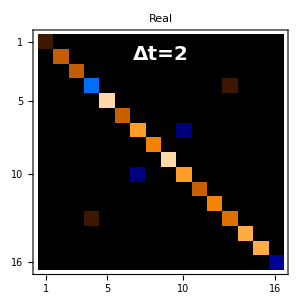
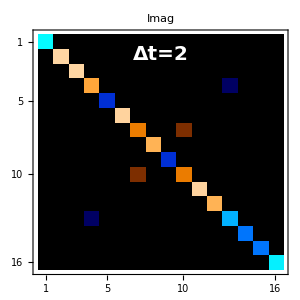

```mathematica
Print@goal
```

```mathematica
order=1;
visTrotter[t,order,"Trotter order "<>ToString[order]<>", Δt="<>ToString[t]]
```

```mathematica
Print@goal
Print[subspace+1]
```

-Graphics--Graphics-

{4,6,7,10,11,13}

```mathematica
Table[{trial,matsubcomp[t][[trial]][[All,"ngates"]]},{trial,10}]
```

{{1,{0,13,21,68,20}},{2,{0,12,52,16}},{3,{0,14,16,55,17}},{4,{0,17,57,16}},{5,{0,17,57,34}},{6,{0,8,13,61,18}},{7,{0,14,54,17}},{8,{0,18,18}},{9,{0,9,9}},{10,{0,11,11}}}

```mathematica
visComp[matsubcomp[t][[6]],"subspace-compiled, t=2, trial6","subdist"]
```

```mathematica
Table[{trial,matfullcomp[t][[trial]][[All,"ngates"]]},{trial,10}]
```

{{1,{0,22,22,41,42,91,53}},{2,{0,21,40,39,42,44,91,46}},{3,{0,20,30,44,93,46}},{4,{0,18,23,26,30,78,31}},{5,{0,17,22,36,42,59,104,56}},{6,{0,22,26,26,74,41}},{7,{0,16,24,31,26,31,32,82,41}},{8,{0,20,40,55,105,56}},{9,{0,20,21,26,26,74,37}},{10,{0,21,33,38,37,37,39,38,86,39}}}

```mathematica
Print@goal
```

-Graphics--Graphics-

```mathematica
visComp[matfullcomp[t][[4]],"full space, t=2, trial4","fulldist"]
```